# 求解符号偏微分方程

## Wolfram 语言专题讲座系列

杨圣汇 
Wolfram Research Inc.

## 总览

本次讲座将覆盖以下内容https://reference.wolfram.com/language/tutorial/DSolvePartialDifferentialEquations.html.zh?source=footerNonehttps://reference.wolfram.com/language/tutorial/DSolvePartialDifferentialEquations.html.zh?source=footerHyperlinkActionRecycledHyperlinkActive

一阶偏微分方程

Transport Equation/迁移方程

标量守恒定律方程

Clairaut Equation / 克洛莱方程

经典偏微分方程

Wave equation/波动方程

Heat equation/传热方程

Laplace equation/拉普拉斯方程

近现代偏微分方程探究

Burgers / 博格斯方程

Black-Scholes 方程

Schrodinger/薛定谔方程

Korteweg-deVries 方程

Sturm-Liouville 本征值问题

Dirichlet 边界条件

Neumann 边界条件

Robin 边界条件

微分特征系统

## 一阶偏微分方程

迁移方程式一阶线性偏微分方程

```mathematica
TransportEquation=D[u[x,t],t]+D[u[x,t],x]==0;
```

```mathematica
TraditionalForm[TransportEquation]//Magnify[#,1.3]&
```

u^(0,1)(x,t)+u^(1,0)(x,t)==0

求该方程的通解

```mathematica
DSolve[TransportEquation,u,{x,t}]
```

{{u→Function[{x,t},C[1][t-x]]}}

如果给定初值条件

```mathematica
sol=DSolve[{TransportEquation,u[x,0]==E^(-x^2)},u,{x,t}]
```

{{u→Function[{x,t},ⅇ^(-(-t+x)^2)]}}

```mathematica
Animate[
Plot[Evaluate[u[x,t]/.sol[[1]]],{x,0,10},
PlotRange->All,Ticks->False,Filling->Axis],
{t,0,10},DefaultDuration->15,AnimationRepetitions->1,SaveDefinitions->True]
```

### 标量守恒定律

该偏微分方程是一个一阶拟线性偏微分方程

```mathematica
ScalarConservationLaw=D[u[x,y],x]+u[x,y]*D[u[x,y],y]==0;
```

```mathematica
TraditionalForm[ScalarConservationLaw]//Magnify[#,1.3]&
```

u(x,y) u^(0,1)(x,y)+u^(1,0)(x,y)==0

通解的表达式是一个隐函数

```mathematica
DSolve[ScalarConservationLaw,u[x,y],{x,y}]
```

Solve[u[x,y]==C[1][x-y/u[x,y]],u[x,y]]

给定初值条件并求解初值问题

```mathematica
DSolve[{ScalarConservationLaw,u[x,0]==1/(x+1)},u,{x,y}]
```

{{u→Function[{x,y},(1+y)/(1+x)]}}

### Clairaut 方程

Clairaut 方程是一阶非线性偏微分方程

```mathematica
ClairautEquation=u[x,y]==x*D[u[x,y],{x}]+y*D[u[x,y],{y}]+(1/2)*(D[u[x,y],{x}]^2+D[u[x,y],{y}]^2);
```

```mathematica
TraditionalForm[ClairautEquation]//Magnify[#,1.3]&
```

u(x,y)==y u^(0,1)(x,y)+x u^(1,0)(x,y)+1/2 ((u^(0,1)(x,y))^2+(u^(1,0)(x,y))^2)

求解偏微分方程

```mathematica
DSolve[ClairautEquation,u,{x,y}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{u→Function[{x,y},x C[1]+y C[2]+1/2 (C[1]^2+C[2]^2)]}}

如果控制其中一个常数 C[2], 变化 C[1], 那么由此产生平面族的包络线也是该偏微分方程的解

```mathematica
Animate[Plot3D[{(1/2)*(c^2+1)+c*x-y/.{c->m},(1/2)*(-x^2-2*y+1)},{x,-20,20},{y,-20,20},PerformanceGoal->"Quality",Mesh->False,PlotRange->{-250,200},Boxed->False,Axes->None],{m,-6,6},DefaultDuration->10,SaveDefinitions->True]
```

DSolve 利用包络线来求解初值问题

```mathematica
sol=DSolve[{ClairautEquation,u[x,0]==1/2 (1-x^2)},u,{x,y}]
```

{{u→Function[{x,y},1/2 (1-x^2+2 y)]}}

## 经典偏微分方程

### 波动方程

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
```

```mathematica
TraditionalForm[weqn]//Magnify[#,1.3]&
```

u^(0,2)(x,t)==u^(2,0)(x,t)

用该方程模拟拨弦震动。弦两端固定

```mathematica
bc={u[0,t]==0,u[1,t]==0};
```

初始条件

```mathematica
ic={u[x,0]==Piecewise[{{3*x,0≤x≤1/3},{(3*(1-x))/2,1/3≤x≤1}}],Derivative[0,1][u][x,0]==0};
```

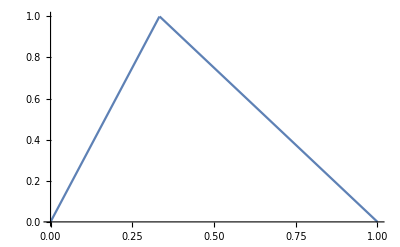

```mathematica
Plot[Piecewise[{{3*x,0≤x≤1/3},{(3*(1-x))/2,1/3≤x≤1}}],{x,0,1}]
```

```mathematica
dsol=DSolve[{weqn,bc,ic},u,{x,t}]/.{K[1]->m}
```

{{u→Function[{x,t},(12 Cos[π t m] Sin[(π m)/3]^3 Sin[π x m])/(π^2 m^2)m1∞]}}

```mathematica
TraditionalForm[u[x,t]/.dsol[[1]]]
```

(12 sin^3((π m)/3) cos(π m t) sin(π m x))/(π^2 m^2)m1∞

抓取前100项

```mathematica
asol[x_,t_]=Activate[u[x,t]/.dsol[[1]]/.{Infinity->100}];
```

可视化弦的额振动情况

```mathematica
Animate[Plot[asol[x,t],{x,0,1},PerformanceGoal->"Speed",PlotRange->{-1.2,1.2},ImageSize->Medium,PlotStyle->Red],{t,0,10},SaveDefinitions->True,AnimationRepetitions->1,DefaultDuration->15]
```

### 传热方程

传热方程是椭圆型线性二阶方程

```mathematica
heqn=D[u[x,t],{t}]==D[u[x,t],{x,2}];
```

```mathematica
TraditionalForm[heqn]//Magnify[#,1.3]&
```

u^(0,1)(x,t)==u^(2,0)(x,t)

用此方程给两端绝缘的长棍温度变化进行建模

```mathematica
bc={Derivative[1,0][u][0,t]==0,Derivative[1,0][u][1,t]==0};
```

初始温度分布

```mathematica
ic=u[x,0]==80*x+20;
```

求解偏微分方程

```mathematica
sol=DSolve[{heqn,bc,ic},u[x,t],{x,t}]
```

{{u[x,t]→60+2 (80 (-1+(-1)^K[1]) ⅇ^(-π^2 t K[1]^2) Cos[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}

抓取前100项

```mathematica
approxsol=Expand[Activate[u[x,t]/.sol[[1]]/.{Infinity->10}]]
```

60-(320 ⅇ^(-π^2 t) Cos[π x])/π^2-(320 ⅇ^(-9 π^2 t) Cos[3 π x])/(9 π^2)-(64 ⅇ^(-25 π^2 t) Cos[5 π x])/(5 π^2)-(320 ⅇ^(-49 π^2 t) Cos[7 π x])/(49 π^2)-(320 ⅇ^(-81 π^2 t) Cos[9 π x])/(81 π^2)

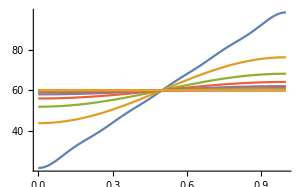

```mathematica
Plot[Evaluate[Table[approxsol,{t,0,0.9,0.07}]],{x,0,1},AxesOrigin->{0,0},PlotRange->All]
```

### Laplace 方程

```mathematica
leqn=Laplacian[u[x,y],{x,y}]==0;
```

```mathematica
TraditionalForm[leqn]//Magnify[#,1.3]&
```

u^(0,2)(x,y)+u^(2,0)(x,y)==0

在长方形区域上求 Dirichlet 边界条件下的解

```mathematica
dcond=DirichletCondition[u[x,y]==Piecewise[{{UnitTriangle[2 x-1],y==0||y==2}},0],True];
```

```mathematica
Ω=Rectangle[{0,0},{1,2}];
```

```mathematica
sol=FullSimplify[DSolve[{leqn,dcond},u[x,y],Element[{x,y},Ω]]]
```

{{u[x,y]→(8 Cosh[π (-1+y) K[1]] Sech[π K[1]] Sin[1/2 π K[1]] Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}

抓取前300项

```mathematica
asol1=Activate[u[x,y]/.sol[[1]]/.{Infinity->300}];
```

```mathematica
Plot3D[Evaluate[asol1],Element[{x,y},Ω],PlotRange->All,MeshFunctions->{#3/E^#3&},Mesh->10,MeshStyle->Blue,Ticks->None,Axes->None,Boxed->False]
```

-Graphics3D-

## 近现代偏微分方程探究

### 博格斯方程

```mathematica
BurgersEquation=D[u[x,t],{t}]+u[x,t]*D[u[x,t],{x}]==ϵ*D[u[x,t],{x,2}];
```

```mathematica
TraditionalForm[BurgersEquation]//Magnify[#,1.3]&
```

u^(0,1)(x,t)+u(x,t) u^(1,0)(x,t)==ϵ u^(2,0)(x,t)

给定初始条件

```mathematica
InitialCondition=u[x,0]==Piecewise[{{1,x<0}}];
```

```mathematica
dsol=DSolveValue[{BurgersEquation,InitialCondition},u[x,t],{x,t}]
```

1/(1+(ⅇ^(-(t-2 x)/(4 ϵ)) (1+Erf[x/(2 √(t ϵ))]))/(1+Erf[(t-x)/(2 √(t ϵ))]))

对于任意 ϵ > 0, 解均光滑

```mathematica
Plot3D[dsol/.{ϵ->1/10},{x,-2,2},{t,0.001,5}]
```

-Graphics3D-

```mathematica
Table[Plot3D[dsol,{x,-2,2},{t,0.001,5},Exclusions->None,Ticks->None],{ϵ,{1/10,1/100,1/1000}}]
```

General::munfl: Exp[-1000.2] is too small to represent as a normalized machine number; precision may be lost.

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Black–Scholes 方程

BS 期权定价模型

```mathematica
BlackScholesModel={-(r*c[t,s])+r*s*D[c[t,s],{s}]+(1/2)*s^2*σ^2*D[c[t,s],{s,2}]+D[c[t,s],{t}]==0,c[T,s]==Max[s-k,0]};
```

```mathematica
MaTeX["\\frac {\\partial c}{\\partial t}+{\\frac {1}{2}}\\sigma ^{2}S^{2}{\\frac {\\partial ^{2}c}{\\partial S^{2}}}+rS{\\frac {\\partial c}{\\partial S}}-r \\cdot c=0"]
```

-Graphics-

```mathematica
dsol=DSolveValue[BlackScholesModel,c[t,s],{t,s}]
```

1/2 ⅇ^(-r T) (-ⅇ^(r t) k Erfc[((t-T) (2 r-σ^2)+2 Log[k]-2 Log[s])/(2 √2 √(-t+T) σ)]+ⅇ^(r T) s Erfc[((t-T) (2 r+σ^2)+2 Log[k]-2 Log[s])/(2 √2 √(-t+T) σ)])

```mathematica
dsol/.{t->0,s->100,k->100,σ->0.7,T->1,r->0.05}
```

29.2027

与 FinancialDerivative 比较结果

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->100.,"Expiration"->1},{"InterestRate"->0.05,"Volatility"->0.7,"CurrentPrice"->100}]
```

29.2027

### 薛定谔方程

shrodinger equation

WolframAlphaQueryResults

```mathematica
eqn = I*ℏ*D[ψ[x, y, t], {t}] ==  -((ℏ^2*Laplacian[ψ[x, y, t], {x, y}])/(2*m));
```

```mathematica
MaTeX[eqn]
```

-Graphics-

给定初始条件

```mathematica
initSum=ψ[x,y,0]==Sqrt[2]*(Sin[2*Pi*x]*Sin[Pi*y]+Sin[Pi*x]*Sin[3*Pi*y]);
```

给定边界条件

```mathematica
bcs={ψ[0,y,t]==0,ψ[1,y,t]==0,ψ[x,1,t]==0,ψ[x,0,t]==0};
```

求解偏微分方程

```mathematica
sol=DSolveValue[{eqn,bcs,initSum},ψ[x,y,t],{x,y,t}]
```

√2 ⅇ^(-(5 ⅈ π^2 t ℏ)/m) (ⅇ^((5 ⅈ π^2 t ℏ)/(2 m)) Sin[2 π x] Sin[π y]+Sin[π x] Sin[3 π y])

```mathematica
ρ[x_,y_,t_]=ComplexExpand[sol*Conjugate[sol]]/.{m->1,xMax->1,yMax->1,ℏ->0.11576762785911278};
```

可视化概率密度函数的随时间的变化

```mathematica
ListAnimate[Table[Plot3D[ρ[x,y,t],{x,0,1},{y,0,1},PlotRange->{0,7}],{t,0,19,0.5}],SaveDefinitions->True]
```

### Korteweg-deVries 方程

K-dV 方程是可积分非线性偏微分方程

```mathematica
KdV=D[u[x,t],{x,3}]+D[u[x,t],{t}]+6*u[x,t]*D[u[x,t],{x}]==0;
```

```mathematica
MaTeX[KdV]
```

-Graphics-

移动的孤波作为偏微分方程的一个解

```mathematica
sol=DSolve[KdV,u[x,t],{x,t}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{u[x,t]→-(-8 C[1]^3+C[2]+12 C[1]^3 Tanh[x C[1]+t C[2]+C[3]]^2)/(6 C[1])}}

通过限定一组常数来得到一个确定的解

```mathematica
psol=Simplify[u[x,t]/.sol[[1]]/.{C[1]->1,C[2]->-4,C[3]->1/4}]
```

2-2 Tanh[1/4-4 t+x]^2

```mathematica
Animate[Plot[psol/.{t->m},{x,-7,15},PlotRange->All,Filling->Axis],{m,1,7},AnimationRepetitions->1,DefaultDuration->30,SaveDefinitions->True]
```

## Sturm-Liouville 特征值问题

### Dirichlet 边界条件

```mathematica
TraditionalForm[{Derivative[2][y][x]+λ*y[x]==0,y[0]==0,y[Pi]==0}]//Magnify[#,1.3]&
```

{y''(x)+λ y(x)==0,y(0)==0,y(π)==0}

```mathematica
sol=DSolve[{Derivative[2][y][x]+λ*y[x]==0,y[0]==0,y[Pi]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Sin[x √λ], n∈ℤ&&n≥1&&λ==n^2}, {0, True}}]}}

抓取前五个本征解并绘图

```mathematica
eigfuns=Table[y[x]/.sol[[1]]//.{n->i,λ->n^2}/.{C[1]->1},{i,5}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x]}

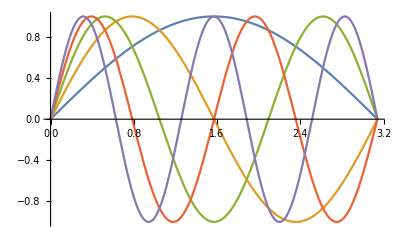

```mathematica
Plot[Evaluate[eigfuns],{x,0,π}]
```

### Neumann 边界条件

```mathematica
TraditionalForm[{Derivative[2][y][x]+λ*y[x]==0,Derivative[1][y][0]==0,Derivative[1][y][Pi]==0}]//Magnify[#,1.4]&
```

{y''(x)+λ y(x)==0,y'(0)==0,y'(π)==0}

```mathematica
sol=DSolve[{Derivative[2][y][x]+λ*y[x]==0,Derivative[1][y][0]==0,Derivative[1][y][Pi]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥0&&λ==n^2}, {0, True}}]}}

抓取前五个本征解并绘图

```mathematica
eigfuns=Table[y[x]/.sol[[1]]//.{n->i,λ->n^2}/.{C[1]->1},{i,0,4}]
```

{1,Cos[x],Cos[2 x],Cos[3 x],Cos[4 x]}

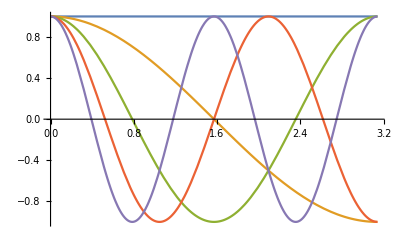

```mathematica
Plot[Evaluate[eigfuns],{x,0,π}]
```

### Robin 边界条件

左边边界条件为 Robin 边界条件 (可以考虑是 Dirichlet 与 Neumann 的加权和 )

```mathematica
TraditionalForm[{Derivative[2][y][x]+λ^2*y[x]==0,Derivative[1][y][0]+y[0]==0,y[1]==0}]//Magnify[#,1.4]&
```

{y''(x)+λ^2 y(x)==0,y'(0)+y(0)==0,y(1)==0}

```mathematica
sol=DSolve[{Derivative[2][y][x]+λ^2*y[x]==0,Derivative[1][y][0]+y[0]==0,y[1]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] (-λ Cos[x λ]+Sin[x λ]), λ Cos[λ]==Sin[λ]}, {0, True}}]}}

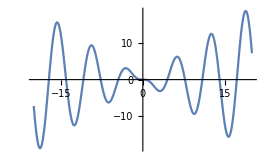

```mathematica
Plot[λ Cos[λ]-Sin[λ],{λ,-20,20}]
```

假设给定 1<λ<10

```mathematica
roots=λ/.Solve[λ*Cos[λ]==Sin[λ]&&1<λ<10,λ];
data=Table[{λ,0},{λ,roots}];
```

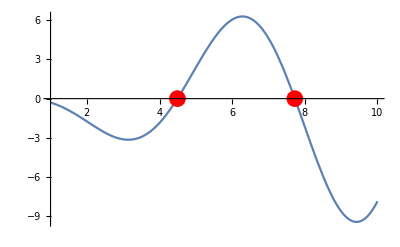

```mathematica
Plot[λ*Cos[λ]-Sin[λ],{λ,1,10},Epilog->{PointSize[0.03],Red,Point[data]}]
```

直接在 DSolveValue 里面加 Assumption

```mathematica
DSolveValue[{Derivative[2][y][x]+λ^2*y[x]==0,Derivative[1][y][0]+y[0]==0,y[1]==0},y[x],x,Assumptions->1<λ<10]
```

Piecewise[{{C[1] (-λ Cos[x λ]+Sin[x λ]), λ==Root4.49Root[{-Sin[#1]+Cos[#1] #1&,4.4934094579090641753}]4.493409457909064||λ==Root7.73Root[{-Sin[#1]+Cos[#1] #1&,7.7252518369377071642}]7.725251836937707}, {0, True}}]

RootObject 是具有任意精度的对象（类似于整数或者 π）

```mathematica
N[Root"4.49"Root[{-Sin[#1]+Cos[#1] #1&,4.49340945790906417530706257624367738757`20.309702343599472}]4.493409457909064,500]
```

4.4934094579090641753078809272803220822155838722900408028958239619269503145971040987290578094558796915217692198610142800856895097383716922678652322815875333643634255776924777218315283356126190621743243209552544584281718198128769916450794366574987465597477701162901897834303180402120789785639552495164930363632701299681005660940581280051337204986035996815212767258392274928680217482017711289563747923607170058554294089965281187713403078704560854465692762092720079044546518194432108647210147346951627478

## 特征值

### DEigensystem

找出 [0,π] 上面最小的四个特征值和对应的特征函数

```mathematica
DEigensystem[{-Laplacian[u[x],{x}],DirichletCondition[u[x]==0,True]},u[x],{x,0,Pi},4]
```

{{1,4,9,16},{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x]}}

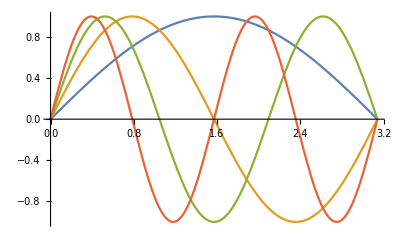

```mathematica
Plot[Evaluate[%[[2]]],{x,0,π}]
```

### 量子谐振子

```mathematica
qho=-((ℏ^2*Laplacian[u[x],{x}])/(2*m))+(1/2)*x^2*(m*ω^2)*u[x];
```

```mathematica
TraditionalForm[qho]//Magnify[#,1.3]&
```

1/2 m x^2 ω^2 u(x)-(ℏ^2 u''(x))/(2 m)

```mathematica
TraditionalForm[({ℰs,efuns}=DEigensystem[qho,u[x],{x,-∞,∞},4,Assumptions->ℏ>0∧m>0∧ω>0,Method->"Normalize"])]//Magnify[#,1.3]&
```

((ω ℏ)/2 | (3 ω ℏ)/2 | (5 ω ℏ)/2 | (7 ω ℏ)/2
((m ω ℏ)^(1/4) ⅇ^(-(m x^2 ω)/(2 ℏ)))/(π^(1/4) √ℏ) | (√2 x ((m ω)/ℏ)^(3/4) ⅇ^(-(m x^2 ω)/(2 ℏ)))/π^(1/4) | ((m ω ℏ)^(1/4) ⅇ^(-(m x^2 ω)/(2 ℏ)) ((4 m x^2 ω)/ℏ-2))/(2 √2 π^(1/4) √ℏ) | ((m ω ℏ)^(1/4) ⅇ^(-(m x^2 ω)/(2 ℏ)) (8 x^3 ((m ω)/ℏ)^(3/2)-12 x √((m ω)/ℏ)))/(4 √3 π^(1/4) √ℏ))

找出四个叠加态的波动方程

```mathematica
TraditionalForm[ψ[x_,t_]=Total[MapThread[(1/2)*#2*E^((I*E*#1*t)/ℏ)&,{ℰs,efuns}]]]//Magnify[#,1.2]&
```

(x ((m ω)/ℏ)^(3/4) ⅇ^(-(m x^2 ω)/(2 ℏ)+3/2 ⅈ ⅇ t ω))/(√2 π^(1/4))+((m ω ℏ)^(1/4) (8 x^3 ((m ω)/ℏ)^(3/2)-12 x √((m ω)/ℏ)) ⅇ^(-(m x^2 ω)/(2 ℏ)+7/2 ⅈ ⅇ t ω))/(8 √3 π^(1/4) √ℏ)+((m ω ℏ)^(1/4) ((4 m x^2 ω)/ℏ-2) ⅇ^(-(m x^2 ω)/(2 ℏ)+5/2 ⅈ ⅇ t ω))/(4 √2 π^(1/4) √ℏ)+((m ω ℏ)^(1/4) ⅇ^(-(m x^2 ω)/(2 ℏ)+1/2 ⅈ ⅇ t ω))/(2 π^(1/4) √ℏ)

偏离平衡态幅度的概率密度函数

```mathematica
ρ[x_,t_]=FullSimplify[
ComplexExpand[ψ[x,t]*Conjugate[ψ[x,t]]/.{m->6.8605,ω->0.4041,ℏ->63.5078}]];
```

概率密度函数随时间的变化

```mathematica
Animate[Plot[ρ[x,t],{x,-25,25},PlotRange->{0,0.16},PlotTheme->"Detailed",FrameLabel->Style[x,FontSize->Larger],PlotLegends->Placed[{HoldForm[ρ][x,NumberForm[t,{3,2}]]},Above]],{t,0.,5.7},AnimationRate->1,SaveDefinitions->True,Alignment->Center]
```

### 长方形区域内的拉普拉斯算子

Dirichlet 边界条件下齐次拉普拉斯算子

```mathematica
{ℒ,ℬ}={-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]};
```

找到最小的八个特征值和对应的特征函数

```mathematica
{vals,funs}=DEigensystem[{ℒ,ℬ},u[x,y],{x,0,Pi},{y,0,Pi},8];
```

```mathematica
vals
```

{2,5,5,8,10,10,13,13}

```mathematica
funs
```

{Sin[x] Sin[y],Sin[2 x] Sin[y],Sin[x] Sin[2 y],Sin[2 x] Sin[2 y],Sin[3 x] Sin[y],Sin[x] Sin[3 y],Sin[3 x] Sin[2 y],Sin[2 x] Sin[3 y]}

```mathematica
Table[Plot3D[f,{x,0,Pi},{y,0,Pi},Boxed->False,Mesh->False,Axes->False],{f,funs}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### 圆柱体上的拉普拉斯算子

在圆柱体中定义Dirichlet 边界条件下齐次拉普拉斯算子

```mathematica
ℒ=-Laplacian[u[x,y,z],{x,y,z}];
```

```mathematica
ℬ=DirichletCondition[u[x,y,z]==0,True];
```

```mathematica
Ω=Cylinder[{{0,0,0},{0,0,5}},2];
```

找出最小的七个特征根和对应的特征函数

```mathematica
{vals,funs}=DEigensystem[{ℒ,ℬ},u[x,y,z],Element[{x,y,z},Ω],7];
```

```mathematica
TraditionalForm[vals[[1;;5]]]
```

{π^2/25+(01)^2/4,(4 π^2)/25+(01)^2/4,π^2/25+(11)^2/4,π^2/25+(11)^2/4,(9 π^2)/25+(01)^2/4}

```mathematica
funs[[1;;2]]//TraditionalForm
```

{sin((π z)/5) 01/2 √(x^2+y^2) 01,sin((2 π z)/5) 01/2 √(x^2+y^2) 01}

```mathematica
DensityPlot3D[Evaluate[N[funs[[7]]]],{x,y,z}∈Ω,Boxed->False,Axes->False,PlotPoints->30]
```

-Graphics3D-

### 圆形鼓面振动

```mathematica
ℒ=-Laplacian[u[x,y],{x,y}];
```

```mathematica
ℬ=DirichletCondition[u[x,y]==0,True];
```

```mathematica
TraditionalForm[TableForm[Transpose[{vals,funs}=DEigensystem[{ℒ,ℬ},u[x,y],Element[{x,y},Disk[]],6]]]]
```

(01)^2 | 001 √(x^2+y^2)
(11)^2 | (x 1√(x^2+y^2) 11)/(√(x^2+y^2))
(11)^2 | (y 1√(x^2+y^2) 11)/(√(x^2+y^2))
(21)^2 | 2√(x^2+y^2) 21 cos(2 tan^-1(x,y))
(21)^2 | 2√(x^2+y^2) 21 sin(2 tan^-1(x,y))
(02)^2 | 002 √(x^2+y^2)

128 个特征函数组合起来模拟鼓面振动情况（收到位于中心的敲击）

## 未来展望

增加积分变换和格林函数方法

增加周期性边界条件和更为复杂的几何约束区域